```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
Run["./run"];
(*MatrixForm[H=ImportArmaBinary["H.bin"]];
MatrixForm[Px=ImportArmaBinary["Px.bin"]];
MatrixForm[Py=ImportArmaBinary["Py.bin"]];*)
MatrixForm[w=ImportArmaBinary["w.bin"][[1]]];
(*MatrixForm[w0=ImportArmaBinary["w0.bin"][[1]]];*)
MatrixForm[psi=ImportArmaBinary["psi.bin"]];
(*Norm[H.Px-Px.H]
Norm[H.Py-Py.H]
Tally[w0,Norm[#1-#2]<1.*^-7&];
Select[%,#[[2]]>1&]*)
```

```mathematica
plotWF[psi0_]:=Module[{psi, max,L,x,y},
max=Max[Abs[psi0]];
L=Sqrt[Length[psi0]/2];
psi=ArrayReshape[psi0,{L,L,2}];
psi=(psi/max+1)/2;
Graphics[{
AbsoluteThickness[4],
Table[
{Blend[{Red,White,Blue},psi[[y+1,x+1,1]]],
Line[{{x,y},{x+1,y}}],
Blend[{Red,White,Blue},psi[[y+1,x+1,2]]],
Line[{{x,y},{x,y+1}}]}
,{x,0,L-1},{y,0,L-1}]
},Background->GrayLevel[0.8]]
]
```

```mathematica
TableForm[Transpose[{Range[1,Length[w0]],w0}]]
```

{2.47202,2.47202}

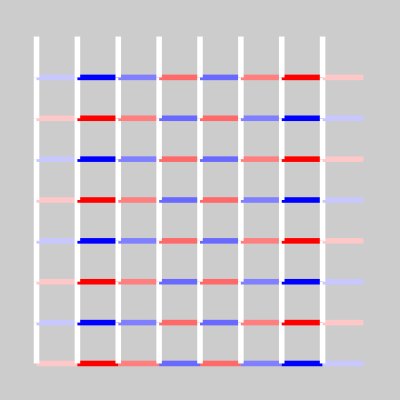

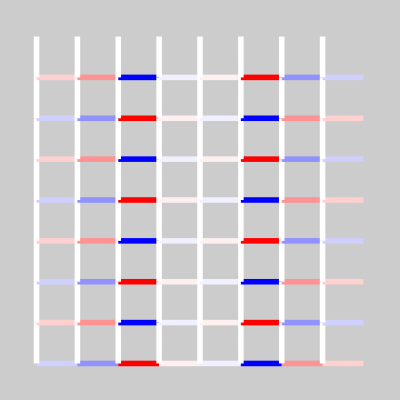

```mathematica
i=127;
{w0[[i]],w0[[i+1]]}
plotWF[psi[[i]]]
plotWF[psi[[i+1]]]
Clear[i]
```